```mathematica
n= 63;precision=17; showNum = 4;
{absc,weights,errweights}=NIntegrate`GaussKronrodRuleData[n,precision];
{gAbsc,gWeights,gErrweights}=NIntegrate`GaussRuleData[n,precision];

gkEvPoints = n+1;
gEvPoints = (n - 1) / 2 +1;
Print[StringForm["Will evaluate  `` .1cGK points, `` Gauss points.", gkEvPoints, gEvPoints]]

clAbsc = Take[Reverse[absc*2 - 1],gkEvPoints];
clGAbsc = Take[Reverse[gAbsc*2 -1], gEvPoints];
clWeights =Take[weights,gkEvPoints];
clGWeights  = Take[gWeights,gEvPoints];

clCompletor = ConstantArray[0, gEvPoints];
clGPaddedWeights = Riffle[clCompletor, clGWeights];

gkAbscCol = Join[{"GK Abscissae"},Take[absc, showNum]];
gkWeightsCol = Join[{"GK Weights"}, Take[weights, showNum]];
gAbscCol = Join[{"G Abscissae"},Take[Riffle[clCompletor,gAbsc],showNum]];
gWeightsCol = Join[{"G Weights"}, Take[Riffle[clCompletor,gWeights],showNum]];
clgkAbscCol = Join[{"GK OCL Abscissae"},Take[clAbsc, showNum]];
clgkAbscTrCol = Join[{"GK Real OCL Absc."},Take[(0.5 - 0.5*#)&/@clAbsc, showNum]];
clgkWeightsCol = Join[{"GK OCL Weights"}, Take[clWeights, showNum]];
clgWeightsCol = Join[{"G OCL Weights"}, Take[clGPaddedWeights,showNum]];

Grid[Transpose[{gkAbscCol,gkWeightsCol,gAbscCol,gWeightsCol, clgkAbscCol,clgkAbscTrCol,clgkWeightsCol,clgWeightsCol}], Frame->All]

Print["Abscissae: "]
clAbsc
Print["GK-Weights: "]
CForm[Transpose[{clWeights, clGPaddedWeights}]]
```

Will evaluate  64 .1cGK points, 32 Gauss points.

GK Abscissae | GK Weights | G Abscissae | G Weights | GK OCL Abscissae | GK Real OCL Absc. | GK OCL Weights | G OCL Weights
0.0000594893317941 | 0.0001602668857576293 | 0 | 0 | 0.9998810213364119 | 0.0000594893 | 0.0001602668857576293 | 0
0.0003585079854381 | 0.0004491353995732647 | 0.00035850798543810981 | 0.0009199372977885421 | 0.9992829840291238 | 0.000358508 | 0.0004491353995732647 | 0.0009199372977885421
0.000966461220035 | 0.00076655616934218326 | 0 | 0 | 0.9980670775599299 | 0.000966461 | 0.00076655616934218326 | 0
0.0018879936110149 | 0.001074300113532651 | 0.0018879936110149457 | 0.002139254173431881 | 0.9962240127779701 | 0.00188799 | 0.001074300113532651 | 0.002139254173431881

Abscissae:

{0.9998810213364119,0.9992829840291238,0.9980670775599299,0.9962240127779701,0.9937758653716868,0.9907285468921895,0.9870733838560134,0.9828088105937272,0.977943724212552,0.97248403469757,0.966428818646282,0.9597794497589419,0.9525431141881967,0.9447261340410098,0.9363308839228898,0.9273609206218432,0.9178236668608461,0.9077263027785316,0.8970734055566613,0.8858703285078534,0.8741252837345546,0.8618464823641237,0.8490402648876593,0.8357135543195028,0.8218755346646491,0.8075354957734568,0.792701295818362,0.7773812629903723,0.7615855963361828,0.7453246483178474,0.7286076184609537,0.7114440995848458,0.6938452823573544,0.6758225281149861,0.6573862277202577,0.6385471058213654,0.619317283377103,0.5997090518776252,0.5797338525277905,0.559403409486285,0.5387306881146957,0.5177288132900332,0.4964101370533716,0.4747872479948044,0.4528738526458268,0.4306837987951116,0.4082302080098307,0.3855263942122479,0.3625866890033956,0.3394255419745844,0.3160566998588286,0.2924940585862514,0.268752449020725,0.2448467932459534,0.2207913155763243,0.1966003467915067,0.1722890839979173,0.147872786357872,0.1233660053816164,0.0987833564469453,0.0741402648096537,0.0494521871161596,0.0247338496538102,0.}

GK-Weights:

List(List(0.0001602668857576293,0),List(0.0004491353995732647,0.0009199372977885421),List(0.00076655616934218326,0),List(0.0010743001135326514,0.0021392541734318809),
   List(0.0013733960249429429,0),List(0.00167489193704677,0.0033551458829800681),List(0.0019804203178136177,0),List(0.002283255071988616,0.0045629843381633282),
   List(0.0025813035029855053,0),List(0.00287857228709358,0.005759688038440021),List(0.0031765645213793029,0),List(0.00347212508138255,0.006942306308057805),
   List(0.0037636509807135553,0),List(0.004053193522587787,0.008107939205169169),List(0.0043417894006603676,0),List(0.00462750544947465,0.009253732230080635),
   List(0.0049091237621183361,0),List(0.005187900015829144,0.010376880629019545),List(0.0054645745296849561,0),List(0.005737783407015212,0.011474635502444967),
   List(0.0060065558697094475,0),List(0.006271746988066909,0.012544310276672493),List(0.0065339128007247288,0),List(0.006792006252581132,0.013583287179548967),
   List(0.0070452215503721709,0),List(0.007294185622520814,0.014589023604140263),List(0.0075393365507710716,0),List(0.007779825526080565,0.015559058311109909),
   List(0.0080149632553483158,0),List(0.008245236920507176,0.016491017441889671),List(0.0084710076063466576,0),List(0.008691561436387231,0.017382620322677939),
   List(0.0089062956831182389,0),List(0.009115608479971126,0.018231685042728645),List(0.0093198106812285531,0),List(0.009518286327300692,0.019036133792174778),
   List(0.0097104998481189873,0),List(0.009896791951874439,0.019793997945772047),List(0.010077441699984176,0),List(0.010251907850988038,0.020503422879833199),
   List(0.010419708802741538,0),List(0.010581148903860852,0.021162672510407911),List(0.010736488731944115,0),List(0.010885246361035789,0.021770133541513795),
   List(0.011026984762456761,0),List(0.01116198673055346,0.022324319412970698),List(0.011290504377039001,0),List(0.01141210431309752,0.022823873938146304),
   List(0.011526387047544722,0),List(0.011633624709532977,0.023267574622691848),List(0.011734068783449215,0),List(0.011827326467637939,0.02365433565613446),
   List(0.011913030232821084,0),List(0.011991449881781019,0.023983210568997566),List(0.012062842641268738,0),List(0.012126850092225866,0.024253394548941924),
   List(0.01218313195760729,0),List(0.012231962348468754,0.024464226410255995),List(0.012273609618331881,0),List(0.012307744577677725,0.02461519021187378),
   List(0.012334049937009303,0),List(0.012352809604639822,0.024705916519959089),List(0.012364307816421746,0),List(0.01236824003585959,0.02473618331196551))

```mathematica
Integrate[(val+4)*(val-3)*(val+0)*(val+1)*(val+4)*(val-3)*(val+0)*(val+1), {val, -5, 5}]
```

8536000/63

```mathematica
N[8536000/63,40]
```

135492.0634920634920634920634920634920635

```mathematica
NumberForm[77853.17460317459,20]
```

77853.17460317458

```mathematica
Integrate[x, {x, 0,2}]
```

64

0.

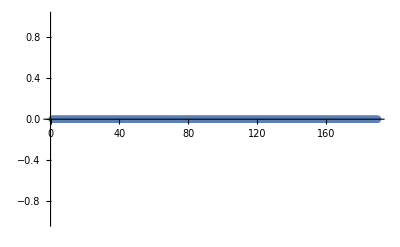

```mathematica
(* Precision measure *)
Length[clAbsc]
abserrs = Table[Abs[
Integrate[x^K,{x, -1, 1}] - 
2*(Function[x, x^K]/@Join[clAbsc, Drop[-clAbsc, -1]] ).Join[clWeights, Drop[clWeights, -1]]],{K, 1, 3*n + 1}];
Max[abserrs]
ListPlot[abserrs ]
```

```mathematica
clAbsc
```

{0.999881021336411862428466639836892446772,0.999282984029123780378936140928944461073,0.998067077559929941635402161134714097941,0.996224012777970108602193361146311353293,0.993775865371686846285577992918029067415,0.990728546892189466810894667204703453054,0.987073383856013413170139516074347437028,0.982808810593727234862511405691611739203,0.977943724212551968824602830027626751502,0.972484034697570022801960678576810948165,0.966428818646281976752230899983412801026,0.959779449758941927070354166258988969165,0.952543114188196747631448391431251227871,0.944726134041009802966375319627500663745,0.936330883922889750480213492576791485618,0.927360920621843205447031381325121569456,0.917823666860846071254304774797622198448,0.907726302778531558036953132915953225548,0.897073405556661321491334260452885275442,0.88587032850785342629029845731336987515,0.874125283734554575059153474541935940645,0.861846482364123719539611839431059953997,0.849040264887659256888984472574877653469,0.835713554319502843471807769615705452824,0.821875534664649062973995165677240810358,0.807535495773456760051465986363243134594,0.792701295818361987072932465797497711508,0.77738126299037233556333018991104275576,0.761585596336182802947384217610143152795,0.745324648317847417829321661037587632315,0.72860761846095367845744702929555004985,0.711444099584845807851431537704014879128,0.693845282357354373575678514318240780899,0.67582252811498609013110331596954450878,0.657386227720257736877667840615196468433,0.638547105821365385000306953873376481233,0.619317283377102995778615584111642564103,0.599709051877625235739008926868799861071,0.579733852527790526805060495168623973006,0.559403409486285013267697800070054696541,0.538730688114695722007438221766173294392,0.517728813290033248124477584526315535577,0.496410137053371624045940182406313896519,0.474787247994804399922212309851494749286,0.452873852645826793137850536896033301402,0.430683798795111600662088933918629982066,0.408230208009830669702877302454042086852,0.385526394212247892477615022274398150275,0.362586689003395569115336215002580552357,0.339425541974584402468834431594315085044,0.316056699858828649365417056518345441137,0.292494058586251440036157155550666923689,0.268752449020725033401128111746493498468,0.244846793245953362748404593924829370148,0.220791315576324339129503787132082363328,0.196600346791506684557627457065717697921,0.172289083997917278786446375839023408001,0.147872786357871968569839096552972943441,0.123366005381616409502774190145451630901,0.09878335644694527952970366945392210344,0.074140264809653734157880548715219749091,0.049452187116159627234233818051807609898,0.024733849653810212120433649137229048164,0.}

255